```mathematica
γ[E_]=(511+E)/511;
β[E_]=Sqrt[(γ[E]^2-1)/γ[E]^2];
Acosta[θ_,β_,A_,B_]=Module[{x1,x2,bp},bp=(1+B)β; x1=((Cos[θ]-bp)/(1-bp Cos[θ]))^2;
 x2=(1-bp^2)/((1-bp Cos[θ])^2);norm=1/18 (16-7 A) ;
(((3 A/8)(1+x1)+(4(1-A)/3)(1-x1))x2)/norm]
```

(18 (1-(1+B)^2 β^2) (4/3 (1-A) (1-(-(1+B) β+Cos[θ])^2/(1-(1+B) β Cos[θ])^2)+3/8 A (1+(-(1+B) β+Cos[θ])^2/(1-(1+B) β Cos[θ])^2)))/((16-7 A) (1-(1+B) β Cos[θ])^2)

```mathematica
PolarPlot[{Acosta[θ, β[1.0],0.29692161307072473, -0.49441756950830446],Acosta[θ, β[5.0],0.36702605456872983, -0.2157627315648924],  Acosta[θ, β[20.0],0.3469531916580861, -0.08823154912917483], Acosta[θ, β[200.0],0.42742069593042026, 0.007354007139954511]},{θ,0,π},PlotLegends-> {"1 keV","5 keV", "20 keV", "200 keV"},DisplayFunction->Identity, ImageSize->"Large"]
```

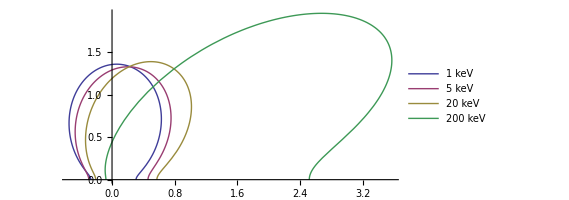

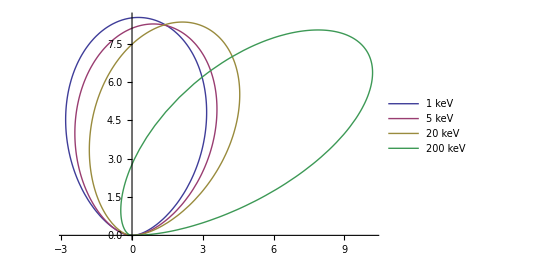

```mathematica
PolarPlot[{2π Sin[θ]Acosta[θ, β[1.0],0.29692161307072473, -0.49441756950830446],2π Sin[θ]Acosta[θ, β[5.0],0.36702605456872983, -0.2157627315648924],  2π Sin[θ]Acosta[θ, β[20.0],0.3469531916580861, -0.08823154912917483], 2π Sin[θ]Acosta[θ, β[200.0],0.42742069593042026, 0.007354007139954511]},{θ,0,π},PlotLegends-> {"1 keV","5 keV", "20 keV", "200 keV"},DisplayFunction->Identity, ImageSize->"Large"]
```

```mathematica
SphericalPlot3D[Acosta[θ, β[1.0],0.29692161307072473, -0.49441756950830446],{θ,0,π},{ϕ,0,2π},PlotLabel->"Nominal",PlotLegends-> {"1 keV" },DisplayFunction->Identity,PerformanceGoal->"Quality"]
```

-Graphics3D-

```mathematica
SphericalPlot3D[Acosta[θ, β[5.0],0.36702605456872983, -0.2157627315648924],{θ,0,π},{ϕ,0,2π},PlotLabel->"Nominal",PlotLegends-> {"5 keV" },DisplayFunction->Identity,PerformanceGoal->"Quality"]
```

-Graphics3D-

```mathematica
SphericalPlot3D[ Acosta[θ, β[20.0],0.3469531916580861, -0.08823154912917483],{θ,0,π},{ϕ,0,2π},PlotLabel->"Nominal",PlotLegends-> {"20 keV" },DisplayFunction->Identity,PerformanceGoal->"Quality"]
```

-Graphics3D-

```mathematica
SphericalPlot3D[Acosta[θ, β[200.0],0.42742069593042026, 0.007354007139954511],{θ,0,π},{ϕ,0,2π},PlotLabel->"Nominal",PlotLegends-> {"200 keV" },DisplayFunction->Identity,PerformanceGoal->"Quality"]
```

-Graphics3D-

```mathematica
Integrate[2π Sin[θ]Acosta[θ,β,A,B],{θ,0,π},Assumptions:>{0<A<1, -1<B<1,0<β<1/(1+B)}]
```

4 π